# Differential Equations: DSolve, NDSolve ancillary: Manipulate. Goal: Solve ordinary differential equations, either symbolically or numerically and plot the solutions. Phase space of simple mechanical systems.

Check out the tutorial on “Differential Equations” on documentation center

```mathematica
Remove["Global`*"]
```

Basic syntax for solving differential equations : DSolve
should contain three arguments: The differential equation (== not =), the function to be solved and the independent variable.

```mathematica
DSolve[f'[x]-λ f[x]==0,f,x]
```

A slightly different format

```mathematica
DSolve[f'[x]-λ f[x]==0,f[x],x]
```

Including initial conditions

```mathematica
DSolve[{f'[x]-λ f[x]==0,f[0]==A},f[x],x]
```

```mathematica
f[x_]=f[x]/.%
```

```mathematica
f[t]
```

```mathematica
f[3.4]
```

```mathematica
Physics Example: Particle falling from a height h0 with a  viscous drag (proportional to velocity)
```

```mathematica
sol=DSolve[{m y''[t]==-m g-b y'[t],y[0]==h0,y'[0]==0},y[t],t]
```

{{y[t]→(ⅇ^(-(b t)/m) (b^2 ⅇ^((b t)/m) h0-g m^2+ⅇ^((b t)/m) g m^2-b ⅇ^((b t)/m) g m t))/b^2}}

```mathematica
h=y[t]/.sol;
```

```mathematica
Simplify[h]
```

{(b^2 h0+(1-ⅇ^(-(b t)/m)) g m^2-b g m t)/b^2}

Example: put in the values for g, m and h0.

```mathematica
h1=h/.{m->1,g->9.8,h0-> 100}
```

{(ⅇ^(-b t) (-9.8+9.8 ⅇ^(b t)+100 b^2 ⅇ^(b t)-9.8 b ⅇ^(b t) t))/b^2}

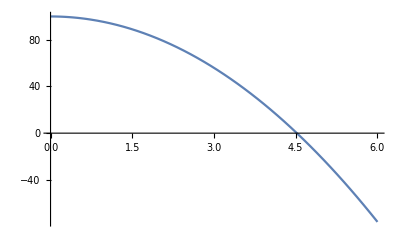

```mathematica
Plot[h1/.{b->0.001},{t,0,6},PlotRange->Full]
```

Plotting for different values of the drag coefficient ‘b’, using the “Manipulate” command

```mathematica
Manipulate[
Plot[h1/.{b->drag},{t,0,20},PlotRange->{0,100}],
{drag,0.001,10}]
```

### DSolve examples

```mathematica
(*Harmonic Oscillator*)
DSolve[x''[t]+k x[t]==0,x[t],t]
```

```mathematica
DSolve[y''[x]+A x^2 y[x]==K y[x],y,x]
```

```mathematica
DSolve[y''[x]+A x y[x]==K y[x],y,x]
```

```mathematica
(*DSolve[y''[x]+A Cos[y[x]]==K y[x],y,x]*)
```

```mathematica
DSolve[y''[t]-A y[t]^2+B==0,y,t]
```

```mathematica
sol=DSolve[{y''[t]-A y[t]==0,y[0]==0},y[t],t]
```

```mathematica
Plot[{y[t]/.sol/.A->1/.C[1]->1},{t,0,2}]
```

```mathematica
Plot[{Im[y[t]/.sol/.A->-1/.C[1]->1]},{t,0,5}]
```

```mathematica
(*Simple pendulum*)
DSolve[x''[t]+k Sin[x[t]]==0,x[t],t]
```

### NDSolve examples:

#### 1. Period of a simple pendulum

```mathematica
Remove["Global`*"]
```

```mathematica
eqn=ϕ''[t]+(2 Pi)^2Sin[ϕ[t]]==0;
```

```mathematica
sol1=NDSolve[{eqn,ϕ[0]==.2,ϕ'[0]==0},ϕ,{t,0,10}];
sol11=NDSolve[{eqn,ϕ[0]==.25,ϕ'[0]==0},ϕ,{t,0,10}];
sol2=NDSolve[{eqn,ϕ[0]==.5 Pi,ϕ'[0]==0},ϕ,{t,0,10}];
sol3=NDSolve[{eqn,ϕ[0]==.9 Pi,ϕ'[0]==0},ϕ,{t,0,10}];
```

```mathematica
Show[Plot[ϕ[t]/.sol1,{t,0,3},PlotStyle->Red,PlotRange->All],
Plot[ϕ[t]/.sol11,{t,0,3},PlotStyle->{Dashed},PlotRange->All]]
```

```mathematica
Show[Plot[ϕ[t]/.sol1,{t,0,3},PlotStyle->Red,PlotRange->All],
Plot[ϕ[t]/.sol11,{t,0,3},PlotStyle->{Dashed},PlotRange->All],Plot[ϕ[t]/.sol2,{t,0,3},PlotStyle->Blue],
Plot[ϕ[t]/.sol3,{t,0,3},PlotStyle->Green]
]
```

```mathematica
FindRoot[ϕ[t]/.sol1,{t,0.25}]
```

```mathematica
FindRoot[ϕ[t]/.sol1,{t,0.25}][[1,2]]
```

```mathematica
t/.FindRoot[ϕ[t]/.sol1,{t,0.25}]
```

```mathematica
Abs[FindRoot[ϕ[t]/.sol1,{t,0.25}][[1,2]]-
FindRoot[ϕ[t]/.sol1,{t,0.75}][[1,2]]]
```

```mathematica
Abs[FindRoot[ϕ[t]/.sol3,{t,0.5}][[1,2]]-
FindRoot[ϕ[t]/.sol3,{t,1.5}][[1,2]]]
```

```mathematica
Clear["Global'*"]
```

Phase space Plots

Check out ”Module”. Can also use “Block” instead of Module. Check that out as well.

```mathematica
(* Pendulum with dissipation *)
 Manipulate[Module[{pend =
    NDSolve[{x'[t] ==   y[t], 
        y'[t] == -γ*y[t]-Sin[x[t]], x[0] == p[[1]], 
        y[0] == p[[2]]}, {x[t], y[t]}, {t, 0, Tend}]},
                   ParametricPlot[Evaluate[{x[t], y[t]} /. pend], {t, 0, Tend}, 
                                  PlotRange -> {{-3 Pi, 3 Pi}, {-5, 5}}]], {{p, {2, 1}}, 
                       Locator}, {{Tend, 10}, 0, 100},{γ,0,1,0.1}]
```

Predator-Prey Model: When Fox meets Rabbit

```mathematica
Manipulate[Module[{foxrabbit =
    NDSolve[{x'[t] ==   x[t]*(1- y[t]), 
        y'[t] == -y[t]*(1 - x[t]), x[0] == p[[1]], 
        y[0] == p[[2]]}, {x[t], y[t]}, {t, 0, Tend}]},
                   ParametricPlot[Evaluate[{x[t], y[t]} /. foxrabbit], {t, 0, Tend}, 
                                  PlotRange -> {{0, 5}, {0, 5}}]], {{p, {2, 1}}, 
                       Locator}, {{Tend, 10}, 0, 100}]
```

Forced Harmonic Oscillator

```mathematica
Manipulate[Module[{forho =
    NDSolve[{x'[t] ==   y[t], 
        y'[t] == - ω^2 x[t]+A Cos[Ω t], x[0] == p[[1]], 
        y[0] == p[[2]]}, {x[t], y[t]}, {t, 0, Tend}]},
                   ParametricPlot[Evaluate[{x[t], y[t]} /. forho], {t, 0, Tend}, 
                                  PlotRange -> {{-5, 5}, {-5, 5}}]], {{p, {2, 1}}, 
                       Locator}, {{Tend, 10}, 0, 100},{ω,.1,4,.1},{A,0,3},{Ω,.1,4,.1}]
```